```mathematica
β[ω_,δ_,t_,ϵ_]:=
β[ω,δ,t,ϵ]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[14],Join[Table[{i,i-1},{i,Range[2,14,1]}],Table[{i,i+1},{i,Range[1,14,1]}],Table[{2n-1,14-2n+2},{n,4}],Table[{14-2n+2,2n-1},{n,3}]]->-t]
```

```mathematica
T1[t_]:=T1[t]=ReplacePart[0*IdentityMatrix[14],Table[{2n,14-2n+1},{n,3}]->t]
```

```mathematica
TT[t_]:=ReplacePart[0*IdentityMatrix[14],Table[{2n,2n},{n,3}]->t]
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_]:=LEFT[ω,δ,t,ϵ]=Module[{J=Inverse[β[ω,0.0001,1,0]],B:=Inverse[β[ω,0.0001,1,0]],T1:=T1[1]},Do[J=Inverse[IdentityMatrix[14]-B.ConjugateTranspose[T1].J.T1].B,10000]; J=J]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_]:=SR[ω,δ,t,ϵ]=Inverse[IdentityMatrix[14]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ].T1[t]].g[ω,δ,t,ϵ]
```

```mathematica
SL[ω_,δ_,t_,ϵ_]:=SL[ω,δ,t,ϵ]=Inverse[IdentityMatrix[14]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ].T1[t]].g[ω,δ,t,ϵ]
```

```mathematica
IL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[14]-SL[ω,δ,t,ϵ].TT[t].SR[ω,δ,t,ϵ].TT[t]].SL[ω,δ,t,ϵ]
```

```mathematica
IR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[14]-SR[ω,δ,t,ϵ].TT[t].SL[ω,δ,t,ϵ].TT[t]].SR[ω,δ,t,ϵ]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_]:= IL[ω,δ,t,ϵ]-ConjugateTranspose[IL[ω,δ,t,ϵ]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_]:= IR[ω,δ,t,ϵ]-ConjugateTranspose[IR[ω,δ,t,ϵ]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_]:= SR[ω,δ,t,ϵ].TT[t].IL[ω,δ,t,ϵ]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_]:= Gnonlocal[ω,δ,t,ϵ]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_]:= Abs[Tr[gdd[ω,δ,t,ϵ].TT[t].grr[ω,δ,t,ϵ].TT[t]-TT[t].GNON[ω,δ,t,ϵ].TT[t].GNON[ω,δ,t,ϵ]]]
```

```mathematica
Table[{ω,tr[ω,0.0001,1,0]},{ω,Range[0,3,0.01]}]
```

{{0.,2.8×10^-7},{0.01,2.8081×10^-7},{0.02,2.83264×10^-7},{0.03,2.87439×10^-7},{0.04,2.93463×10^-7},{0.05,3.01536×10^-7},{0.06,3.11935×10^-7},{0.07,3.25045×10^-7},{0.08,3.41391×10^-7},{0.09,3.61694×10^-7},{0.1,3.86954×10^-7},{0.11,4.18578×10^-7},{0.12,4.58598×10^-7},{0.13,5.10023×10^-7},{0.14,5.77474×10^-7},{0.15,6.68349×10^-7},{0.16,7.95126×10^-7},{0.17,9.803×10^-7},{0.18,1.26801×10^-6},{0.19,1.75544×10^-6},{0.2,2.69447×10^-6},{0.21,4.92698×10^-6},{0.22,0.0000129427},{0.23,0.000120119},{0.24,0.999916},{0.25,0.999991},{0.26,0.999997},{0.27,0.999998},{0.28,0.999999},{0.29,0.999998},{0.3,0.999998},{0.31,0.999999},{0.32,0.999997},{0.33,0.999996},{0.34,0.999992},{0.35,0.999991},{0.36,0.999979},{0.37,1.},{0.38,0.999977},{0.39,0.999993},{0.4,1.},{0.41,1.00011},{0.42,1.99989},{0.43,1.99999},{0.44,1.99996},{0.45,1.99997},{0.46,1.99993},{0.47,1.99995},{0.48,2.},{0.49,1.99991},{0.5,1.99997},{0.51,1.99996},{0.52,1.99987},{0.53,1.99983},{0.54,1.99991},{0.55,1.99993},{0.56,1.99994},{0.57,1.99984},{0.58,1.99974},{0.59,1.99973},{0.6,2.},{0.61,1.99955},{0.62,1.99989},{0.63,1.99989},{0.64,1.99968},{0.65,1.99982},{0.66,1.99948},{0.67,1.99991},{0.68,1.99989},{0.69,1.99954},{0.7,1.99927},{0.71,1.99967},{0.72,1.99949},{0.73,1.99989},{0.74,1.99976},{0.75,1.99905},{0.76,1.99897},{0.77,1.99942},{0.78,1.999},{0.79,1.99988},{0.8,1.99966},{0.81,1.99912},{0.82,1.99884},{0.83,1.99924},{0.84,1.99955},{0.85,2.99948},{0.86,2.99989},{0.87,2.99905},{0.88,2.99958},{0.89,2.99872},{0.9,2.99894},{0.91,2.99892},{0.92,2.99869},{0.93,2.99929},{0.94,2.99986},{0.95,2.99869},{0.96,2.99996},{0.97,2.99879},{0.98,2.99943},{0.99,2.99974},{1.,2.99861},{1.01,2.99969},{1.02,2.99935},{1.03,2.99878},{1.04,2.99987},{1.05,2.99862},{1.06,2.99977},{1.07,2.99896},{1.08,2.99893},{1.09,2.99979},{1.1,2.99998},{1.11,2.99971},{1.12,2.99981},{1.13,2.99885},{1.14,2.99929},{1.15,2.99907},{1.16,2.99979},{1.17,2.99976},{1.18,2.99993},{1.19,2.99926},{1.2,2.9984},{1.21,2.99863},{1.22,2.99904},{1.23,2.99903},{1.24,2.99859},{1.25,2.9997},{1.26,2.99975},{1.27,2.9993},{1.28,2.99816},{1.29,2.99987},{1.3,2.9997},{1.31,2.99907},{1.32,2.99969},{1.33,2.99842},{1.34,2.99909},{1.35,2.99822},{1.36,2.99867},{1.37,2.99857},{1.38,2.99862},{1.39,2.99974},{1.4,2.99909},{1.41,2.99947},{1.42,2.99872},{1.43,2.99916},{1.44,2.9989},{1.45,2.99892},{1.46,2.99899},{1.47,2.99912},{1.48,2.99832},{1.49,2.99967},{1.5,2.99925},{1.51,2.99903},{1.52,2.99909},{1.53,2.9993},{1.54,2.99814},{1.55,2.99972},{1.56,2.9995},{1.57,2.99849},{1.58,2.99995},{1.59,2.99892},{1.6,2.99918},{1.61,2.99872},{1.62,2.99952},{1.63,2.99876},{1.64,2.99882},{1.65,2.99946},{1.66,2.99967},{1.67,2.99913},{1.68,2.99845},{1.69,2.99951},{1.7,2.99872},{1.71,2.99986},{1.72,2.99979},{1.73,2.99983},{1.74,2.9991},{1.75,2.99962},{1.76,2.9987},{1.77,1.99889},{1.78,1.999},{1.79,1.99976},{1.8,1.99948},{1.81,1.99953},{1.82,1.99995},{1.83,1.99901},{1.84,1.99892},{1.85,1.99929},{1.86,1.99957},{1.87,1.99987},{1.88,1.99929},{1.89,1.99986},{1.9,1.99989},{1.91,1.99957},{1.92,1.99994},{1.93,1.99966},{1.94,1.99977},{1.95,1.99985},{1.96,1.99934},{1.97,1.99941},{1.98,1.99977},{1.99,1.99968},{2.,1.99971},{2.01,1.99976},{2.02,1.99964},{2.03,1.99979},{2.04,1.99944},{2.05,1.99959},{2.06,1.99946},{2.07,1.99998},{2.08,2.},{2.09,1.99975},{2.1,1.99992},{2.11,1.99982},{2.12,2.},{2.13,1.99961},{2.14,1.99986},{2.15,1.99989},{2.16,1.99972},{2.17,1.99983},{2.18,1.99982},{2.19,2.},{2.2,1.99988},{2.21,1.9998},{2.22,1.99979},{2.23,1.99981},{2.24,1.99983},{2.25,1.99984},{2.26,1.99983},{2.27,1.99983},{2.28,1.99992},{2.29,1.99997},{2.3,1.99991},{2.31,1.99987},{2.32,1.99988},{2.33,1.99998},{2.34,1.9999},{2.35,1.99993},{2.36,1.99998},{2.37,1.99998},{2.38,1.99995},{2.39,1.99997},{2.4,1.99993},{2.41,1.99986},{2.42,1.00005},{2.43,0.999975},{2.44,0.999973},{2.45,0.999975},{2.46,0.999974},{2.47,0.999979},{2.48,0.999999},{2.49,1.},{2.5,0.999996},{2.51,1.},{2.52,0.999991},{2.53,0.999999},{2.54,0.999998},{2.55,0.999994},{2.56,0.999998},{2.57,0.999997},{2.58,0.999999},{2.59,1.},{2.6,0.999998},{2.61,0.999999},{2.62,1.},{2.63,1.},{2.64,0.999999},{2.65,1.},{2.66,1.},{2.67,1.},{2.68,1.},{2.69,1.},{2.7,1.},{2.71,1.},{2.72,1.},{2.73,1.},{2.74,1.},{2.75,1.},{2.76,1.},{2.77,1.},{2.78,0.999999},{2.79,0.999999},{2.8,0.999999},{2.81,0.999998},{2.82,0.999997},{2.83,0.999992},{2.84,0.999958},{2.85,0.000496198},{2.86,0.0000165305},{2.87,4.97473×10^-6},{2.88,2.35363×10^-6},{2.89,1.36412×10^-6},{2.9,8.87821×10^-7},{2.91,6.22951×10^-7},{2.92,4.6079×10^-7},{2.93,3.54437×10^-7},{2.94,2.8098×10^-7},{2.95,2.28152×10^-7},{2.96,1.88907×10^-7},{2.97,1.58966×10^-7},{2.98,1.35611×10^-7},{2.99,1.17044×10^-7},{3.,1.02043×10^-7},{3.01,8.97514×10^-8},{3.02,7.9554×10^-8},{3.03,7.10012×10^-8},{3.04,6.37576×10^-8},{3.05,5.75691×10^-8},{3.06,5.22402×10^-8},{3.07,4.76186×10^-8},{3.08,4.35846×10^-8},{3.09,4.00423×10^-8},{3.1,3.69149×10^-8},{3.11,3.414×10^-8},{3.12,3.16663×10^-8},{3.13,2.94518×10^-8},{3.14,2.74614×10^-8},{3.15,2.56657×10^-8},{3.16,2.40401×10^-8},{3.17,2.25637×10^-8},{3.18,2.12187×10^-8},{3.19,1.99899×10^-8},{3.2,1.88644×10^-8},{3.21,1.78307×10^-8},{3.22,1.68791×10^-8},{3.23,1.60012×10^-8},{3.24,1.51895×10^-8},{3.25,1.44374×10^-8},{3.26,1.37393×10^-8},{3.27,1.30901×10^-8},{3.28,1.24853×10^-8},{3.29,1.1921×10^-8},{3.3,1.13935×10^-8},{3.31,1.08998×10^-8},{3.32,1.0437×10^-8},{3.33,1.00026×10^-8},{3.34,9.59432×10^-9},{3.35,9.21007×10^-9},{3.36,8.84801×10^-9},{3.37,8.50646×10^-9},{3.38,8.1839×10^-9},{3.39,7.87895×10^-9},{3.4,7.59034×10^-9},{3.41,7.31692×10^-9},{3.42,7.05766×10^-9},{3.43,6.81158×10^-9},{3.44,6.5778×10^-9},{3.45,6.35553×10^-9},{3.46,6.14401×10^-9},{3.47,5.94257×10^-9},{3.48,5.75058×10^-9},{3.49,5.56745×10^-9},{3.5,5.39265×10^-9},{3.51,5.22569×10^-9},{3.52,5.06609×10^-9},{3.53,4.91344×10^-9},{3.54,4.76734×10^-9},{3.55,4.62743×10^-9},{3.56,4.49335×10^-9},{3.57,4.36479×10^-9},{3.58,4.24145×10^-9},{3.59,4.12306×10^-9},{3.6,4.00935×10^-9},{3.61,3.90008×10^-9},{3.62,3.79503×10^-9},{3.63,3.69399×10^-9},{3.64,3.59674×10^-9},{3.65,3.50311×10^-9},{3.66,3.41293×10^-9},{3.67,3.32601×10^-9},{3.68,3.24222×10^-9},{3.69,3.1614×10^-9},{3.7,3.08341×10^-9},{3.71,3.00813×10^-9},{3.72,2.93544×10^-9},{3.73,2.86521×10^-9},{3.74,2.79734×10^-9},{3.75,2.73172×10^-9},{3.76,2.66827×10^-9},{3.77,2.60687×10^-9},{3.78,2.54746×10^-9},{3.79,2.48994×10^-9},{3.8,2.43423×10^-9},{3.81,2.38026×10^-9},{3.82,2.32797×10^-9},{3.83,2.27728×10^-9},{3.84,2.22812×10^-9},{3.85,2.18045×10^-9},{3.86,2.13419×10^-9},{3.87,2.08931×10^-9},{3.88,2.04573×10^-9},{3.89,2.00342×10^-9},{3.9,1.96232×10^-9},{3.91,1.92239×10^-9},{3.92,1.88359×10^-9},{3.93,1.84588×10^-9},{3.94,1.80921×10^-9},{3.95,1.77355×10^-9},{3.96,1.73887×10^-9},{3.97,1.70512×10^-9},{3.98,1.67227×10^-9},{3.99,1.64031×10^-9},{4.,1.60918×10^-9}}

```mathematica
Clear[k00]
```

```mathematica
f00:=f00=Interpolation[%15]
```

```mathematica
k00:=k00=Table[{ω,f00[ω]},{ω,Range[0,3,0.001]}]
```

```mathematica
k00
```

{{0.,2.8×10^-7},{0.001,2.80009×10^-7},{0.002,2.80034×10^-7},{0.003,2.80075×10^-7},{0.004,2.80131×10^-7},{0.005,2.80204×10^-7},{0.006,2.80293×10^-7},{0.007,2.80398×10^-7},3985,{3.993,1.63088×10^-9},{3.994,1.62776×10^-9},{3.995,1.62464×10^-9},{3.996,1.62153×10^-9},{3.997,1.61843×10^-9},{3.998,1.61534×10^-9},{3.999,1.61226×10^-9},{4.,1.60918×10^-9}}
 |  |  |  |

```mathematica
Pri[ω_]:=tr[ω,0.0001,1,0]
```

```mathematica
Pri[1]
```

3.

```mathematica
Clear[f14,f28,f42,f56,f70,f84,f100]
```

```mathematica
f14:=f14=Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/1imp.dat"]]
f28:=f28=Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/2imp.dat"]]
f42:=f42=Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/3imp.dat"]]
f56:=f56=Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/4imp.dat"]]
f70:=f70=Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/5imp.dat"]]
f84:=f84=Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/6imp.dat"]]
f100:=f100=Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/7imp.dat"]](*
f114:=f114=Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/114imp100.csv"]]*)
```

```mathematica
k14:=k14=Table[{ω,f14[ω]},{ω,0,3,0.001}]
k28:=k28=Table[{ω,f28[ω]},{ω,0,3,0.001}]
k42:=k42=Table[{ω,f42[ω]},{ω,0,3,0.001}]
k56:=k56=Table[{ω,f56[ω]},{ω,0,3,0.001}]
k70:=k70=Table[{ω,f70[ω]},{ω,0,3,0.001}]
k84:=k84=Table[{ω,f84[ω]},{ω,0,3,0.001}]
k100:=k100=Table[{ω,f100[ω]},{ω,0,3,0.001}]
(*k114:=k114=Table[{ω,f114[ω]},{ω,0,3,0.001}]*)
```

```mathematica
k56
```

{{0.,2.56796×10^-7},{0.001,2.53949×10^-7},{0.002,2.51492×10^-7},{0.003,2.49406×10^-7},{0.004,2.47674×10^-7},{0.005,2.46276×10^-7},{0.006,2.45194×10^-7},{0.007,2.4441×10^-7},2985,{2.993,1.06932×10^-7},{2.994,1.05457×10^-7},{2.995,1.04035×10^-7},{2.996,1.02665×10^-7},{2.997,1.01348×10^-7},{2.998,1.00084×10^-7},{2.999,9.88732×10^-8},{3.,9.77163×10^-8}}
 |  |  |  |

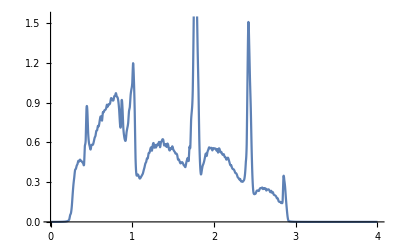

```mathematica
ListLinePlot[k84]
```

```mathematica
f[ω_]:={k00[[ω*1000+1]][[2]],k14[[ω*1000+1]][[2]],k28[[ω*1000+1]][[2]],k42[[ω*1000+1]][[2]],k56[[ω*1000+1]][[2]],k70[[ω*1000+1]][[2]],k84[[ω*1000+1]][[2]],k100[[ω*1000+1]][[2]](*,k114[[ω*1000+1]][[2]]*)}
```

```mathematica
f[1.2]
```

{2.9984,2.341,1.90322,1.5979,1.35776,1.19211,1.0317,0.913721}

```mathematica
Clear[ββ,ψ]
```

```mathematica
ββ[ω_]:=Table[Table[(*{i,j,*)(f[ω][[j]]-f[ω][[i]])/(j-i)(*}*),{i,1,j-1}],{j,1,4}]
```

```mathematica
ββ[1.303]
```

{{},{-0.590446},{-0.507891,-0.425336},{-0.437931,-0.361673,-0.29801}}

```mathematica
ψ[ω_]:=ψ[ω]=-Mean[Flatten[ββ[ω]]]
```

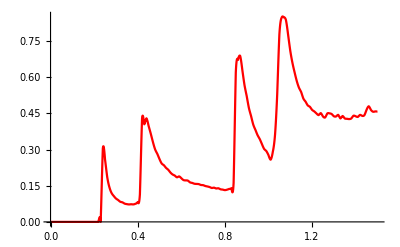

```mathematica
ListLinePlot[Table[{ω,Abs[ψ[ω]]},{ω,Range[0,1.5,0.001]}],PlotStyle->Red]
```

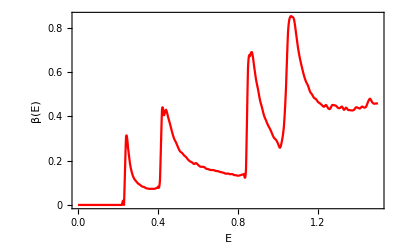

```mathematica
Show[%93,FrameTicks->{{{0,.2,0.4,0.6,0.8},None},{Automatic,None}},FrameLabel->{{HoldForm[β[Ε]],None},{HoldForm[Ε],None}},LabelStyle->{FontFamily->"Times New Roman",16,GrayLevel[0]},Frame->True,(*Epilog->{Text[Style["(b)","Times New Roman",18],{0.2,2.8}]},*)PlotStyle->{Red}]
```

```mathematica
ListLinePlot[Table[{ω,ψ[ω]},{ω,Range[0,3.0,0.001]}]]
```

```mathematica
deltae[ϵ1_,ω_]:=Module[{Tin=T1[1],T=TT[1]},
tra:=Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{1,1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{2,2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{3,3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{4,4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{5,5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{6,6}}->ω+ⅈ*0.0001-ϵ1]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{7,7}}->ω+ⅈ*0.0001-ϵ1]]],
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{8,8}}->ω+ⅈ*0.0001-ϵ1]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{9,9}}->ω+ⅈ*0.0001-ϵ1]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{10,10}}->ω+ⅈ*0.0001-ϵ1]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{11,11}}->ω+ⅈ*0.0001-ϵ1]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{12,12}}->ω+ⅈ*0.0001-ϵ1]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{13,13}}->ω+ⅈ*0.0001-ϵ1]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-ϵ1]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]},
lista={{imp,imp9,imp4,imp3,imp6,imp2,imp11,imp13,imp13,imp,imp,imp10,imp5,imp5,imp,imp5,imp14,imp14,imp6,imp,imp1,imp10,imp5,imp6,imp10,imp12,imp,imp,imp2,imp14,imp,imp2,imp,imp1,imp2,imp9,imp7,imp8,imp3,imp,imp,imp,imp10,imp6,imp14,imp,imp6,imp1,imp,imp5,imp3,imp,imp,imp13,imp,imp8,imp2,imp6,imp10,imp4,imp,imp,imp4,imp13,imp,imp13,imp,imp2,imp11,imp7,imp1,imp8,imp7,imp,imp,imp5,imp9,imp,imp7,imp3,imp13,imp,imp,imp5,imp13,imp9,imp4,imp,imp10,imp12,imp7,imp,imp6,imp,imp14,imp5,imp1,imp13,imp1,imp}};b=Module[{},
(*Print[Dimensions[list]];*)sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,4}]; J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]];
b];
tra]
```

```mathematica
deltae[0.5,1.128]
```

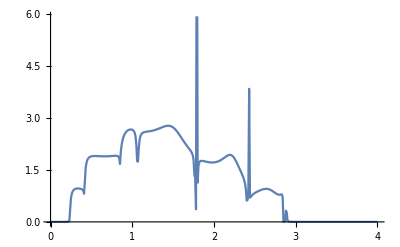

```mathematica
ListLinePlot[Table[{ω,deltae[0.5,ω]},{ω,Range[0,3,0.01]}]]
```

```mathematica
Table[{ω,ψ[ω]*(k00[[ω*1000*1]]-deltae[0.5,ω])},{ω,Range[0.0,1.6,0.001]}]
```

{{0.,-1.41741×10^-13},{0.001,-5.91542×10^-14},{0.002,-1.43563×10^-14},{0.003,-2.69457×10^-17},{0.004,-1.13366×10^-14},{0.005,-4.58577×10^-14},{0.006,-1.03481×10^-13},{0.007,-1.86337×10^-13},{0.008,-2.20803×10^-13},{0.009,-9.27184×10^-14},{0.01,7.2024×10^-14},{0.011,2.83903×10^-13},{0.012,5.553×10^-13},{0.013,9.00439×10^-13},{0.014,1.33534×10^-12},{0.015,1.87776×10^-12},{0.016,2.54716×10^-12},{0.017,3.36466×10^-12},{0.018,4.35296×10^-12},{0.019,5.53637×10^-12},{0.02,6.94073×10^-12},{0.021,8.55872×10^-12},{0.022,1.0447×10^-11},{0.023,1.26388×10^-11},{0.024,1.51697×10^-11},{0.025,1.80784×10^-11},{0.026,2.14067×10^-11},{0.027,2.51992×10^-11},{0.028,2.95042×10^-11},{0.029,3.4373×10^-11},{0.03,3.98609×10^-11},{0.031,4.62337×10^-11},{0.032,5.33658×10^-11},{0.033,6.13084×10^-11},{0.034,7.01124×10^-11},{0.035,7.98283×10^-11},{0.036,9.05061×10^-11},{0.037,1.02195×10^-10},{0.038,1.14944×10^-10},{0.039,1.288×10^-10},{0.04,1.43808×10^-10},{0.041,1.58917×10^-10},{0.042,1.75212×10^-10},{0.043,1.92811×10^-10},{0.044,2.1185×10^-10},{0.045,2.32479×10^-10},{0.046,2.54865×10^-10},{0.047,2.79191×10^-10},{0.048,3.0566×10^-10},{0.049,3.34494×10^-10},{0.05,3.65937×10^-10},{0.051,4.04078×10^-10},{0.052,4.4549×10^-10},{0.053,4.90212×10^-10},{0.054,5.38265×10^-10},{0.055,5.89646×10^-10},{0.056,6.44331×10^-10},{0.057,7.02267×10^-10},{0.058,7.63376×10^-10},{0.059,8.27549×10^-10},{0.06,8.94645×10^-10},{0.061,9.53207×10^-10},{0.062,1.01413×10^-9},{0.063,1.07796×10^-9},{0.064,1.14531×10^-9},{0.065,1.21687×10^-9},{0.066,1.29343×10^-9},{0.067,1.37586×10^-9},{0.068,1.46512×10^-9},{0.069,1.5623×10^-9},{0.07,1.66857×10^-9},{0.071,1.80749×10^-9},{0.072,1.95837×10^-9},{0.073,2.12125×10^-9},{0.074,2.29607×10^-9},{0.075,2.4827×10^-9},{0.076,2.68094×10^-9},{0.077,2.89049×10^-9},{0.078,3.11099×10^-9},{0.079,3.34195×10^-9},{0.08,3.58281×10^-9},{0.081,3.80871×10^-9},{0.082,4.04295×10^-9},{0.083,4.28625×10^-9},{0.084,4.5394×10^-9},{0.085,4.80327×10^-9},{0.086,5.0788×10^-9},{0.087,5.36703×10^-9},{0.088,5.66907×10^-9},{0.089,5.98616×10^-9},{0.09,6.3196×10^-9},{0.091,6.67286×10^-9},{0.092,7.04546×10^-9},{0.093,7.43893×10^-9},{0.094,7.85492×10^-9},{0.095,8.29519×10^-9},{0.096,8.76163×10^-9},{0.097,9.25627×10^-9},{0.098,9.78129×10^-9},{0.099,1.0339×10^-8},{0.1,1.09319×10^-8},{0.101,1.15759×10^-8},{0.102,1.22606×10^-8},{0.103,1.2988×10^-8},{0.104,1.37602×10^-8},{0.105,1.45797×10^-8},{0.106,1.54488×10^-8},{0.107,1.63699×10^-8},{0.108,1.73459×10^-8},{0.109,1.83793×10^-8},{0.11,1.9473×10^-8},{0.111,2.06599×10^-8},{0.112,2.19132×10^-8},{0.113,2.32342×10^-8},{0.114,2.46241×10^-8},{0.115,2.6084×10^-8},{0.116,2.7615×10^-8},{0.117,2.9218×10^-8},{0.118,3.08939×10^-8},{0.119,3.26434×10^-8},{0.12,3.4467×10^-8},{0.121,3.6279×10^-8},{0.122,3.81663×10^-8},{0.123,4.01347×10^-8},{0.124,4.21905×10^-8},{0.125,4.43407×10^-8},{0.126,4.65925×10^-8},{0.127,4.89539×10^-8},{0.128,5.14335×10^-8},{0.129,5.40404×10^-8},{0.13,5.67844×10^-8},{0.131,5.97389×10^-8},{0.132,6.28522×10^-8},{0.133,6.61326×10^-8},{0.134,6.95885×10^-8},{0.135,7.32287×10^-8},{0.136,7.70626×10^-8},{0.137,8.11001×10^-8},{0.138,8.53515×10^-8},{0.139,8.98278×10^-8},{0.14,9.45404×10^-8},{0.141,9.90947×10^-8},{0.142,1.03911×10^-7},{0.143,1.09031×10^-7},{0.144,1.14498×10^-7},{0.145,1.20361×10^-7},{0.146,1.26675×10^-7},{0.147,1.33497×10^-7},{0.148,1.40892×10^-7},{0.149,1.48929×10^-7},{0.15,1.57685×10^-7},{0.151,1.69006×10^-7},{0.152,1.81218×10^-7},{0.153,1.943×10^-7},{0.154,2.08227×10^-7},{0.155,2.22967×10^-7},{0.156,2.38478×10^-7},{0.157,2.54713×10^-7},{0.158,2.71614×10^-7},{0.159,2.89114×10^-7},{0.16,3.07135×10^-7},{0.161,3.21516×10^-7},{0.162,3.36214×10^-7},{0.163,3.51383×10^-7},{0.164,3.672×10^-7},{0.165,3.8386×10^-7},{0.166,4.01586×10^-7},{0.167,4.20624×10^-7},{0.168,4.41251×10^-7},{0.169,4.63776×10^-7},{0.17,4.88541×10^-7},{0.171,5.2061×10^-7},{0.172,5.55757×10^-7},{0.173,5.94139×10^-7},{0.174,6.35918×10^-7},{0.175,6.81265×10^-7},{0.176,7.30356×10^-7},{0.177,7.83376×10^-7},{0.178,8.4052×10^-7},{0.179,9.01987×10^-7},{0.18,9.6799×10^-7},{0.181,1.0326×10^-6},{0.182,1.10211×10^-6},{0.183,1.17718×10^-6},{0.184,1.25854×10^-6},{0.185,1.34699×10^-6},{0.186,1.44343×10^-6},{0.187,1.54887×10^-6},{0.188,1.66442×10^-6},{0.189,1.79133×10^-6},{0.19,1.93097×10^-6},{0.191,2.08671×10^-6},{0.192,2.25849×10^-6},{0.193,2.44809×10^-6},{0.194,2.65752×10^-6},{0.195,2.88898×10^-6},{0.196,3.14496×10^-6},{0.197,3.4282×10^-6},{0.198,3.74178×10^-6},{0.199,4.08914×10^-6},{0.2,4.47412×10^-6},{0.201,4.90468×10^-6},{0.202,5.38213×10^-6},{0.203,5.91165×10^-6},{0.204,6.49907×10^-6},{0.205,7.15095×10^-6},{0.206,7.87469×10^-6},{0.207,8.67863×10^-6},{0.208,9.57223×10^-6},{0.209,0.0000105662},{0.21,0.0000116729},{0.211,0.000012588},{0.212,0.0000136296},{0.213,0.0000148368},{0.214,0.0000162569},{0.215,0.0000179469},{0.216,0.0000199753},{0.217,0.0000224254},{0.218,0.0000253977},{0.219,0.0000290152},{0.22,0.0000334278},{0.221,0.000144549},{0.222,0.000266156},{0.223,0.000392344},{0.224,0.000515103},{0.225,0.000623621},{0.226,0.000703286},{0.227,0.00073424},{0.228,0.000689196},{0.229,0.00052998},{0.23,0.000201741},{0.231,-0.0012267},{0.232,-0.00323433},{0.233,-0.00607264},{0.234,-0.00978023},{0.235,0.202307},{0.236,0.250275},{0.237,0.293549},{0.238,0.334289},{0.239,0.371695},{0.24,0.40488},{0.241,0.409843},{0.242,0.410326},{0.243,0.406852},{0.244,0.399941},{0.245,0.390109},{0.246,0.377868},{0.247,0.363721},{0.248,0.348166},{0.249,0.331685},{0.25,0.314746},{0.251,0.305524},{0.252,0.296107},{0.253,0.28674},{0.254,0.278126},{0.255,0.27491},{0.256,0.104718},{0.257,0.298587},{0.258,0.279191},{0.259,0.267001},{0.26,0.251711},{0.261,0.241693},{0.262,0.233136},{0.263,0.230677},{0.264,0.230623},{0.265,0.210214},{0.266,0.200735},{0.267,0.194863},{0.268,0.206979},{0.269,0.208265},{0.27,0.190087},{0.271,0.215683},{0.272,0.228152},{0.273,0.212579},{0.274,0.20176},{0.275,0.201831},{0.276,0.17332},{0.277,0.157635},{0.278,0.193896},{0.279,0.209679},{0.28,0.198096},{0.281,0.190023},{0.282,0.18659},{0.283,0.195737},{0.284,0.144496},{0.285,0.0710986},{0.286,0.0932992},{0.287,0.0978798},{0.288,0.0921057},{0.289,0.110932},{0.29,0.135378},{0.291,0.151219},{0.292,0.159615},{0.293,0.162469},{0.294,0.159428},{0.295,0.146356},{0.296,0.112938},{0.297,0.0620068},{0.298,0.0556408},{0.299,0.0831454},{0.3,0.100392},{0.301,0.104812},{0.302,0.103984},{0.303,0.110003},{0.304,0.1268},{0.305,0.144332},{0.306,0.1566},{0.307,0.163855},{0.308,0.158829},{0.309,0.157095},{0.31,0.159489},{0.311,0.152766},{0.312,0.128402},{0.313,0.0828747},{0.314,0.0290443},{0.315,0.0130212},{0.316,0.0307345},{0.317,0.0463642},{0.318,0.047111},{0.319,0.0338524},{0.32,0.0207298},{0.321,0.0304909},{0.322,0.0589659},{0.323,0.0859489},{0.324,0.104352},{0.325,0.114919},{0.326,0.118734},{0.327,0.114813},{0.328,0.0983342},{0.329,0.0606414},{0.33,0.019551},{0.331,0.0412664},{0.332,0.0873501},{0.333,0.116984},{0.334,0.133796},{0.335,0.137081},{0.336,0.130133},{0.337,0.125503},{0.338,0.122687},{0.339,0.121778},{0.34,0.123564},{0.341,0.129804},{0.342,0.129995},{0.343,0.0950934},{0.344,0.0430581},{0.345,0.0234484},{0.346,0.0545164},{0.347,0.0874341},{0.348,0.107034},{0.349,0.116099},{0.35,0.11737},{0.351,0.111779},{0.352,0.0981047},{0.353,0.0751149},{0.354,0.0450553},{0.355,0.0195309},{0.356,0.0142907},{0.357,0.0293577},{0.358,0.0509213},{0.359,0.0689964},{0.36,0.0806982},{0.361,0.0860751},{0.362,0.0865031},{0.363,0.0835119},{0.364,0.0790586},{0.365,0.0753633},{0.366,0.0740803},{0.367,0.0753516},{0.368,0.0778324},{0.369,0.079677},{0.37,0.0794222},{0.371,0.076433},{0.372,0.0702461},{0.373,0.0611354},{0.374,0.0500893},{0.375,0.0390445},{0.376,0.0307355},{0.377,0.0275999},{0.378,0.030103},{0.379,0.0362021},{0.38,0.0427709},{0.381,0.0473513},{0.382,0.0489704},{0.383,0.0477109},{0.384,0.0442604},{0.385,0.0395793},{0.386,0.0347197},{0.387,0.030691},{0.388,0.0282841},{0.389,0.0278347},{0.39,0.0290242},{0.391,0.0308056},{0.392,0.032127},{0.393,0.0321994},{0.394,0.0309598},{0.395,0.0290269},{0.396,0.0273792},{0.397,0.0270026},{0.398,0.0286455},{0.399,0.0327007},{0.4,0.0391818},{0.401,0.0460523},{0.402,0.0539215},{0.403,0.0622523},{0.404,0.0706576},{0.405,0.0788997},{0.406,0.0868088},{0.407,0.0941561},{0.408,0.100538},{0.409,0.105351},{0.41,0.107978},{0.411,0.118624},{0.412,0.12607},{0.413,0.137646},{0.414,0.192449},{0.415,0.622199},{0.416,0.759817},{0.417,0.925257},{0.418,0.902662},{0.419,0.885663},{0.42,0.895365},{0.421,0.911235},{0.422,0.96913},{0.423,1.06327},{0.424,1.18209},{0.425,1.04353},{0.426,0.915554},{0.427,0.8316},{0.428,0.823789},{0.429,0.907254},{0.43,1.06795},{0.431,0.97415},{0.432,0.767528},{0.433,0.580787},{0.434,0.428987},{0.435,0.323938},{0.436,0.284327},{0.437,0.366712},{0.438,0.944208},{0.439,1.20324},{0.44,1.11113},{0.441,0.61963},{0.442,0.582841},{0.443,0.523631},{0.444,0.776016},{0.445,1.14988},{0.446,0.733235},{0.447,0.115013},{0.448,0.0553385},{0.449,0.291648},{0.45,0.841767},{0.451,0.937111},{0.452,1.03976},{0.453,0.998504},{0.454,0.78618},{0.455,0.843277},{0.456,1.07144},{0.457,1.18025},{0.458,1.16112},{0.459,1.03808},{0.46,1.17801},{0.461,1.13007},{0.462,1.13606},{0.463,1.15499},{0.464,1.15799},{0.465,1.15829},{0.466,1.12512},{0.467,1.10285},{0.468,1.10831},{0.469,1.11332},{0.47,1.10326},{0.471,1.09171},{0.472,1.07653},{0.473,1.00216},{0.474,0.997473},{0.475,1.07178},{0.476,0.90228},{0.477,0.748039},{0.478,0.635156},{0.479,0.571028},{0.48,0.558684},{0.481,0.610697},{0.482,0.755617},{0.483,1.01638},{0.484,0.741728},{0.485,0.578288},{0.486,0.523168},{0.487,0.487818},{0.488,0.444111},{0.489,0.425244},{0.49,0.491066},{0.491,0.598752},{0.492,0.665461},{0.493,0.676785},{0.494,0.646428},{0.495,0.596029},{0.496,0.55748},{0.497,0.565304},{0.498,0.627616},{0.499,0.710258},{0.5,0.768975},{0.501,0.783136},{0.502,0.761346},{0.503,0.728944},{0.504,0.71595},{0.505,0.734424},{0.506,0.76904},{0.507,0.797334},{0.508,0.807051},{0.509,0.794373},{0.51,0.7562},{0.511,0.686709},{0.512,0.575256},{0.513,0.44435},{0.514,0.37658},{0.515,0.401627},{0.516,0.457005},{0.517,0.502754},{0.518,0.533885},{0.519,0.55511},{0.52,0.571437},{0.521,0.585349},{0.522,0.600829},{0.523,0.619526},{0.524,0.641196},{0.525,0.661126},{0.526,0.667476},{0.527,0.652325},{0.528,0.63119},{0.529,0.621419},{0.53,0.622476},{0.531,0.629342},{0.532,0.635028},{0.533,0.635978},{0.534,0.629758},{0.535,0.614795},{0.536,0.590405},{0.537,0.556632},{0.538,0.513225},{0.539,0.457251},{0.54,0.38005},{0.541,0.270703},{0.542,0.163911},{0.543,0.150807},{0.544,0.217684},{0.545,0.302487},{0.546,0.390826},{0.547,0.478383},{0.548,0.556533},{0.549,0.616696},{0.55,0.652352},{0.551,0.659789},{0.552,0.627885},{0.553,0.556204},{0.554,0.474548},{0.555,0.432942},{0.556,0.442047},{0.557,0.473241},{0.558,0.501956},{0.559,0.51832},{0.56,0.520557},{0.561,0.509393},{0.562,0.48917},{0.563,0.464195},{0.564,0.438426},{0.565,0.414309},{0.566,0.393432},{0.567,0.379687},{0.568,0.38002},{0.569,0.396773},{0.57,0.422026},{0.571,0.444047},{0.572,0.456272},{0.573,0.456069},{0.574,0.443458},{0.575,0.42023},{0.576,0.389438},{0.577,0.353594},{0.578,0.311395},{0.579,0.259117},{0.58,0.208462},{0.581,0.201765},{0.582,0.260208},{0.583,0.349037},{0.584,0.43005},{0.585,0.488851},{0.586,0.523786},{0.587,0.536357},{0.588,0.528714},{0.589,0.504629},{0.59,0.471344},{0.591,0.438144},{0.592,0.415683},{0.593,0.406731},{0.594,0.407675},{0.595,0.413008},{0.596,0.418757},{0.597,0.422943},{0.598,0.424564},{0.599,0.422634},{0.6,0.415975},{0.601,0.404015},{0.602,0.387937},{0.603,0.372628},{0.604,0.365469},{0.605,0.370137},{0.606,0.381343},{0.607,0.389137},{0.608,0.386995},{0.609,0.375193},{0.61,0.360733},{0.611,0.35599},{0.612,0.37043},{0.613,0.40452},{0.614,0.449004},{0.615,0.493386},{0.616,0.531844},{0.617,0.562881},{0.618,0.586992},{0.619,0.605183},{0.62,0.618429},{0.621,0.626917},{0.622,0.63189},{0.623,0.633803},{0.624,0.632938},{0.625,0.629413},{0.626,0.623194},{0.627,0.614106},{0.628,0.601838},{0.629,0.585942},{0.63,0.565797},{0.631,0.539823},{0.632,0.506874},{0.633,0.462873},{0.634,0.399684},{0.635,0.31299},{0.636,0.246844},{0.637,0.253836},{0.638,0.278636},{0.639,0.286787},{0.64,0.284967},{0.641,0.286961},{0.642,0.300907},{0.643,0.326902},{0.644,0.357518},{0.645,0.384489},{0.646,0.403079},{0.647,0.411898},{0.648,0.411221},{0.649,0.401907},{0.65,0.385217},{0.651,0.362111},{0.652,0.3398},{0.653,0.327538},{0.654,0.333214},{0.655,0.355635},{0.656,0.385583},{0.657,0.413964},{0.658,0.436139},{0.659,0.451045},{0.66,0.459149},{0.661,0.463479},{0.662,0.461859},{0.663,0.453889},{0.664,0.438849},{0.665,0.41646},{0.666,0.388558},{0.667,0.360869},{0.668,0.341346},{0.669,0.333686},{0.67,0.33391},{0.671,0.333636},{0.672,0.328419},{0.673,0.315786},{0.674,0.296345},{0.675,0.274496},{0.676,0.25853},{0.677,0.256291},{0.678,0.267505},{0.679,0.282853},{0.68,0.29174},{0.681,0.288571},{0.682,0.273199},{0.683,0.24979},{0.684,0.224808},{0.685,0.205005},{0.686,0.195679},{0.687,0.199166},{0.688,0.213803},{0.689,0.234654},{0.69,0.256344},{0.691,0.275963},{0.692,0.292103},{0.693,0.304911},{0.694,0.314758},{0.695,0.321814},{0.696,0.32601},{0.697,0.327138},{0.698,0.324968},{0.699,0.319376},{0.7,0.310495},{0.701,0.298274},{0.702,0.284817},{0.703,0.272326},{0.704,0.263419},{0.705,0.260094},{0.706,0.262495},{0.707,0.268485},{0.708,0.274334},{0.709,0.27572},{0.71,0.268241},{0.711,0.248747},{0.712,0.21771},{0.713,0.192012},{0.714,0.197777},{0.715,0.231541},{0.716,0.268635},{0.717,0.297049},{0.718,0.31628},{0.719,0.328559},{0.72,0.335781},{0.721,0.338872},{0.722,0.338809},{0.723,0.336067},{0.724,0.331032},{0.725,0.32407},{0.726,0.315539},{0.727,0.305741},{0.728,0.294869},{0.729,0.282998},{0.73,0.27013},{0.731,0.255592},{0.732,0.239962},{0.733,0.22283},{0.734,0.203553},{0.735,0.181978},{0.736,0.160077},{0.737,0.14351},{0.738,0.139767},{0.739,0.151241},{0.74,0.171272},{0.741,0.190554},{0.742,0.201672},{0.743,0.202431},{0.744,0.194031},{0.745,0.180316},{0.746,0.167194},{0.747,0.160668},{0.748,0.16369},{0.749,0.174934},{0.75,0.19113},{0.751,0.209505},{0.752,0.229374},{0.753,0.249485},{0.754,0.267746},{0.755,0.282077},{0.756,0.291363},{0.757,0.295737},{0.758,0.296548},{0.759,0.296265},{0.76,0.297867},{0.761,0.303461},{0.762,0.311946},{0.763,0.319727},{0.764,0.322507},{0.765,0.317082},{0.766,0.302186},{0.767,0.27948},{0.768,0.254851},{0.769,0.23717},{0.77,0.232132},{0.771,0.237024},{0.772,0.245177},{0.773,0.250485},{0.774,0.249727},{0.775,0.24194},{0.776,0.227762},{0.777,0.209426},{0.778,0.190695},{0.779,0.17549},{0.78,0.165438},{0.781,0.159875},{0.782,0.157163},{0.783,0.158371},{0.784,0.165415},{0.785,0.178226},{0.786,0.194328},{0.787,0.210884},{0.788,0.226416},{0.789,0.240926},{0.79,0.255072},{0.791,0.268431},{0.792,0.281166},{0.793,0.291814},{0.794,0.298383},{0.795,0.298798},{0.796,0.291199},{0.797,0.274306},{0.798,0.248927},{0.799,0.221706},{0.8,0.207885},{0.801,0.221474},{0.802,0.255641},{0.803,0.291958},{0.804,0.319252},{0.805,0.335516},{0.806,0.34224},{0.807,0.341203},{0.808,0.333684},{0.809,0.320566},{0.81,0.302666},{0.811,0.280775},{0.812,0.257326},{0.813,0.235046},{0.814,0.216609},{0.815,0.202949},{0.816,0.191658},{0.817,0.177209},{0.818,0.153975},{0.819,0.122518},{0.82,0.0968644},{0.821,0.0979482},{0.822,0.1279},{0.823,0.16692},{0.824,0.197853},{0.825,0.215092},{0.826,0.219457},{0.827,0.213946},{0.828,0.202385},{0.829,0.189077},{0.83,0.177914},{0.831,0.162668},{0.832,0.151837},{0.833,0.143174},{0.834,0.134921},{0.835,0.127287},{0.836,0.12289},{0.837,0.125818},{0.838,0.139096},{0.839,0.162661},{0.84,0.194223},{0.841,0.260892},{0.842,0.333692},{0.843,0.411339},{0.844,0.496474},{0.845,0.59654},{0.846,0.726295},{0.847,0.922686},{0.848,2.13994},{0.849,2.47801},{0.85,2.77487},{0.851,2.9454},{0.852,3.07624},{0.853,3.1633},{0.854,3.21056},{0.855,3.23074},{0.856,3.20382},{0.857,3.11489},{0.858,2.94283},{0.859,2.70395},{0.86,2.49122},{0.861,2.35078},{0.862,1.65483},{0.863,1.59463},{0.864,1.48509},{0.865,1.31093},{0.866,1.093},{0.867,0.874684},{0.868,0.812014},{0.869,3.10248},{0.87,2.65847},{0.871,2.60774},{0.872,2.22134},{0.873,3.06093},{0.874,2.11735},{0.875,2.2706},{0.876,2.5741},{0.877,2.48156},{0.878,2.2201},{0.879,2.32369},{0.88,3.02915},{0.881,2.75597},{0.882,2.99468},{0.883,2.57742},{0.884,2.21843},{0.885,2.51619},{0.886,2.29339},{0.887,2.16038},{0.888,1.9708},{0.889,1.4357},{0.89,1.4584},{0.891,1.52616},{0.892,1.90306},{0.893,2.22633},{0.894,2.24219},{0.895,2.05272},{0.896,1.95835},{0.897,2.13267},{0.898,2.38001},{0.899,2.58745},{0.9,2.58959},{0.901,2.45523},{0.902,2.40721},{0.903,2.47554},{0.904,2.51164},{0.905,2.32386},{0.906,2.28894},{0.907,2.30789},{0.908,2.24324},{0.909,2.03519},{0.91,1.6916},{0.911,1.47593},{0.912,1.58731},{0.913,1.79801},{0.914,1.95239},{0.915,2.01583},{0.916,2.00484},{0.917,1.94774},{0.918,1.86191},{0.919,1.74902},{0.92,1.64268},{0.921,1.66362},{0.922,1.85349},{0.923,2.07946},{0.924,2.23087},{0.925,2.18269},{0.926,2.16596},{0.927,1.95607},{0.928,1.73235},{0.929,1.63172},{0.93,1.67155},{0.931,1.75683},{0.932,1.8121},{0.933,1.81894},{0.934,1.78644},{0.935,1.73104},{0.936,1.66665},{0.937,1.59828},{0.938,1.51786},{0.939,1.40884},{0.94,1.28793},{0.941,1.26428},{0.942,1.37871},{0.943,1.5071},{0.944,1.57849},{0.945,1.59138},{0.946,1.56434},{0.947,1.52405},{0.948,1.50243},{0.949,1.5234},{0.95,1.57904},{0.951,1.62378},{0.952,1.60681},{0.953,1.51562},{0.954,1.40433},{0.955,1.39559},{0.956,1.54524},{0.957,1.70424},{0.958,1.75131},{0.959,1.70003},{0.96,1.59431},{0.961,1.46748},{0.962,1.33467},{0.963,1.20825},{0.964,1.09724},{0.965,1.00824},{0.966,0.94644},{0.967,0.917022},{0.968,0.924923},{0.969,0.967997},{0.97,1.02641},{0.971,1.06651},{0.972,1.07627},{0.973,1.05999},{0.974,1.0473},{0.975,1.07512},{0.976,1.12905},{0.977,1.1727},{0.978,1.19351},{0.979,1.19389},{0.98,1.17996},{0.981,1.1632},{0.982,1.14328},{0.983,1.12325},{0.984,1.10394},{0.985,1.0836},{0.986,1.05734},{0.987,1.01603},{0.988,0.946257},{0.989,0.840619},{0.99,0.739518},{0.991,0.742744},{0.992,0.852489},{0.993,0.960797},{0.994,1.01646},{0.995,1.02079},{0.996,0.989381},{0.997,0.941913},{0.998,0.895251},{0.999,0.853089},{1.,0.811473},{1.001,0.775465},{1.002,0.761902},{1.003,0.786043},{1.004,0.852164},{1.005,0.945901},{1.006,1.03898},{1.007,1.10269},{1.008,1.11734},{1.009,1.07766},{1.01,1.00622},{1.011,0.959849},{1.012,0.958531},{1.013,0.953769},{1.014,0.890976},{1.015,0.763984},{1.016,0.673665},{1.017,0.728096},{1.018,0.843957},{1.019,0.931976},{1.02,0.975525},{1.021,0.985728},{1.022,1.01838},{1.023,1.12346},{1.024,1.25246},{1.025,1.33914},{1.026,1.36957},{1.027,1.34739},{1.028,1.27741},{1.029,1.2325},{1.03,1.39995},{1.031,1.60959},{1.032,1.72601},{1.033,1.72009},{1.034,1.48475},{1.035,1.33405},{1.036,1.60707},{1.037,1.6138},{1.038,1.99307},{1.039,2.40483},{1.04,2.34047},{1.041,2.14171},{1.042,2.68619},{1.043,3.05363},{1.044,3.07605},{1.045,3.29355},{1.046,2.42791},{1.047,2.50373},{1.048,2.85296},{1.049,3.01342},{1.05,3.63177},{1.051,3.72187},{1.052,3.39194},{1.053,3.71942},{1.054,3.65634},{1.055,3.35485},{1.056,3.32307},{1.057,3.72849},{1.058,3.25951},{1.059,3.37314},{1.06,3.66418},{1.061,3.87447},{1.062,3.99107},{1.063,3.66646},{1.064,3.63057},{1.065,3.604},{1.066,3.59415},{1.067,3.38871},{1.068,3.55631},{1.069,3.51014},{1.07,3.4638},{1.071,3.43826},{1.072,3.45371},{1.073,3.39544},{1.074,3.36966},{1.075,3.34404},{1.076,3.32174},{1.077,3.3009},{1.078,3.28433},{1.079,3.28994},{1.08,3.51297},{1.081,3.66389},{1.082,3.15669},{1.083,3.36219},{1.084,3.6516},{1.085,3.3785},{1.086,3.33639},{1.087,3.09529},{1.088,3.11882},{1.089,3.31062},{1.09,3.30308},{1.091,3.29579},{1.092,3.31185},{1.093,3.41473},{1.094,2.7933},{1.095,3.2026},{1.096,3.18595},{1.097,3.20681},{1.098,3.28371},{1.099,3.26659},{1.1,3.24116},{1.101,3.28656},{1.102,3.18959},{1.103,3.14513},{1.104,3.12208},{1.105,3.16287},{1.106,3.27149},{1.107,3.15253},{1.108,3.09858},{1.109,3.17537},{1.11,3.00303},{1.111,3.18752},{1.112,2.95057},{1.113,2.8125},{1.114,2.72424},{1.115,2.70616},{1.116,3.04032},{1.117,2.53565},{1.118,2.46717},{1.119,2.44799},{1.12,2.45185},{1.121,2.47852},{1.122,2.5321},{1.123,2.63223},{1.124,2.79636},{1.125,3.01635},{1.126,2.72189},{1.127,1.96839},{1.128,2.23453},{1.129,2.70519},{1.13,2.85087},{1.131,2.81223},{1.132,2.70077},{1.133,2.55101},{1.134,2.28874},{1.135,1.86083},{1.136,2.18768},{1.137,2.57997},{1.138,2.56319},{1.139,2.43323},{1.14,2.36925},{1.141,2.42788},{1.142,2.5766},{1.143,2.75944},{1.144,2.73416},{1.145,2.59195},{1.146,2.49845},{1.147,2.46122},{1.148,2.50415},{1.149,2.70124},{1.15,2.40921},{1.151,2.1204},{1.152,2.62019},{1.153,2.63614},{1.154,2.65641},{1.155,2.55303},{1.156,2.1217},{1.157,2.06323},{1.158,2.43124},{1.159,2.55669},{1.16,2.5259},{1.161,2.51406},{1.162,2.54222},{1.163,2.58402},{1.164,2.61434},{1.165,2.61677},{1.166,2.57949},{1.167,2.49651},{1.168,2.38337},{1.169,2.29239},{1.17,2.26096},{1.171,2.2416},{1.172,2.14592},{1.173,1.93359},{1.174,1.80328},{1.175,1.86888},{1.176,1.95715},{1.177,1.99935},{1.178,1.99856},{1.179,1.96605},{1.18,1.91319},{1.181,1.85531},{1.182,1.80525},{1.183,1.77229},{1.184,1.75706},{1.185,1.75399},{1.186,1.75364},{1.187,1.74222},{1.188,1.70017},{1.189,1.60759},{1.19,1.48459},{1.191,1.42894},{1.192,1.46125},{1.193,1.482},{1.194,1.46062},{1.195,1.46674},{1.196,1.542},{1.197,1.62693},{1.198,1.69917},{1.199,1.77632},{1.2,1.86891},{1.201,1.97338},{1.202,2.0747},{1.203,2.15989},{1.204,2.22008},{1.205,2.24976},{1.206,2.24492},{1.207,2.20065},{1.208,2.10816},{1.209,1.9461},{1.21,1.66031},{1.211,1.23679},{1.212,1.10706},{1.213,1.30766},{1.214,1.48546},{1.215,1.60679},{1.216,1.69105},{1.217,1.74799},{1.218,1.78689},{1.219,1.82262},{1.22,1.86446},{1.221,1.90069},{1.222,1.9126},{1.223,1.89675},{1.224,1.89035},{1.225,1.96583},{1.226,2.09848},{1.227,2.19704},{1.228,2.23778},{1.229,2.231},{1.23,2.19135},{1.231,2.13648},{1.232,2.0721},{1.233,2.00213},{1.234,1.92844},{1.235,1.85423},{1.236,1.78513},{1.237,1.72816},{1.238,1.68861},{1.239,1.66843},{1.24,1.67533},{1.241,1.73869},{1.242,1.86255},{1.243,1.95345},{1.244,1.9666},{1.245,1.91408},{1.246,1.80991},{1.247,1.67023},{1.248,1.52982},{1.249,1.43931},{1.25,1.41778},{1.251,1.42619},{1.252,1.41052},{1.253,1.35059},{1.254,1.27932},{1.255,1.27926},{1.256,1.37092},{1.257,1.47656},{1.258,1.55528},{1.259,1.61514},{1.26,1.66675},{1.261,1.70648},{1.262,1.71295},{1.263,1.65747},{1.264,1.53177},{1.265,1.45496},{1.266,1.61292},{1.267,1.8628},{1.268,2.054},{1.269,2.17854},{1.27,2.25243},{1.271,2.28366},{1.272,2.28184},{1.273,2.2504},{1.274,2.19028},{1.275,2.10185},{1.276,1.99044},{1.277,1.87781},{1.278,1.8094},{1.279,1.81835},{1.28,1.86042},{1.281,1.84199},{1.282,1.68813},{1.283,1.41834},{1.284,1.20487},{1.285,1.19147},{1.286,1.31763},{1.287,1.48625},{1.288,1.64738},{1.289,1.78349},{1.29,1.88894},{1.291,1.95453},{1.292,1.97733},{1.293,1.94452},{1.294,1.84158},{1.295,1.69345},{1.296,1.63909},{1.297,1.75847},{1.298,1.91019},{1.299,2.00099},{1.3,2.02591},{1.301,1.9989},{1.302,1.9285},{1.303,1.84333},{1.304,1.79328},{1.305,1.80023},{1.306,1.82119},{1.307,1.78825},{1.308,1.6561},{1.309,1.58567},{1.31,1.731},{1.311,1.80943},{1.312,1.81947},{1.313,1.83022},{1.314,1.86906},{1.315,1.93222},{1.316,2.00503},{1.317,2.07345},{1.318,2.1244},{1.319,2.14023},{1.32,2.09612},{1.321,1.97722},{1.322,1.82528},{1.323,1.70522},{1.324,1.63267},{1.325,1.58384},{1.326,1.53485},{1.327,1.46832},{1.328,1.34608},{1.329,1.03399},{1.33,1.27367},{1.331,1.35162},{1.332,1.36035},{1.333,1.35023},{1.334,1.31711},{1.335,1.25967},{1.336,1.18859},{1.337,1.1178},{1.338,1.05902},{1.339,1.0626},{1.34,1.27777},{1.341,1.67457},{1.342,1.96202},{1.343,2.10705},{1.344,2.19025},{1.345,2.25077},{1.346,2.29168},{1.347,2.24428},{1.348,2.21524},{1.349,2.21118},{1.35,2.25107},{1.351,2.13324},{1.352,1.85794},{1.353,1.66083},{1.354,1.65393},{1.355,1.64301},{1.356,1.57642},{1.357,1.49634},{1.358,1.45445},{1.359,1.45772},{1.36,1.48129},{1.361,1.51637},{1.362,1.56784},{1.363,1.61473},{1.364,1.62683},{1.365,1.59723},{1.366,1.54274},{1.367,1.4981},{1.368,1.49863},{1.369,1.54503},{1.37,1.59115},{1.371,1.55043},{1.372,1.30434},{1.373,1.45389},{1.374,1.70989},{1.375,1.79245},{1.376,1.81803},{1.377,1.82209},{1.378,1.81533},{1.379,1.80213},{1.38,1.78544},{1.381,1.77076},{1.382,1.75989},{1.383,1.75914},{1.384,1.77877},{1.385,1.83492},{1.386,1.94225},{1.387,2.07091},{1.388,2.12509},{1.389,2.07824},{1.39,1.98669},{1.391,1.87433},{1.392,1.73612},{1.393,1.56472},{1.394,1.40788},{1.395,1.37901},{1.396,1.48591},{1.397,1.60963},{1.398,1.67451},{1.399,1.66828},{1.4,1.6178},{1.401,1.56402},{1.402,1.53116},{1.403,1.51976},{1.404,1.51083},{1.405,1.47724},{1.406,1.38913},{1.407,1.25942},{1.408,1.29206},{1.409,1.50065},{1.41,1.64665},{1.411,1.65996},{1.412,1.51881},{1.413,1.46333},{1.414,1.7606},{1.415,1.90399},{1.416,1.94368},{1.417,1.9587},{1.418,1.97155},{1.419,1.9835},{1.42,1.99003},{1.421,1.98747},{1.422,1.9728},{1.423,1.94448},{1.424,1.90164},{1.425,1.84437},{1.426,1.77474},{1.427,1.69806},{1.428,1.62381},{1.429,1.56431},{1.43,1.52879},{1.431,1.5104},{1.432,1.48004},{1.433,1.3998},{1.434,1.46525},{1.435,1.66473},{1.436,1.73599},{1.437,1.78184},{1.438,1.82051},{1.439,1.8467},{1.44,1.8576},{1.441,1.85496},{1.442,1.83468},{1.443,1.79402},{1.444,1.72753},{1.445,1.62004},{1.446,1.41413},{1.447,1.06061},{1.448,1.17254},{1.449,1.46155},{1.45,1.61368},{1.451,1.67015},{1.452,1.66042},{1.453,1.6231},{1.454,1.63028},{1.455,1.71708},{1.456,1.79923},{1.457,1.77882},{1.458,1.61395},{1.459,1.55508},{1.46,1.73116},{1.461,1.83649},{1.462,1.8771},{1.463,1.89114},{1.464,1.8931},{1.465,1.88411},{1.466,1.8561},{1.467,1.79245},{1.468,1.67542},{1.469,1.54332},{1.47,1.52833},{1.471,1.57918},{1.472,1.55959},{1.473,1.48439},{1.474,1.48207},{1.475,1.68241},{1.476,1.92043},{1.477,1.93145},{1.478,1.58871},{1.479,1.26983},{1.48,1.44893},{1.481,1.72582},{1.482,1.96385},{1.483,2.12783},{1.484,2.22253},{1.485,2.26381},{1.486,2.26306},{1.487,2.2277},{1.488,2.17222},{1.489,2.12966},{1.49,2.1191},{1.491,2.10868},{1.492,2.05086},{1.493,1.9108},{1.494,1.65306},{1.495,1.32818},{1.496,1.21905},{1.497,1.3431},{1.498,1.49767},{1.499,1.65636},{1.5,1.81599},{1.501,1.95455},{1.502,2.06031},{1.503,2.13255},{1.504,2.17565},{1.505,2.19452},{1.506,2.19427},{1.507,2.185},{1.508,2.19272},{1.509,2.25623},{1.51,2.36694},{1.511,2.33782},{1.512,2.3141},{1.513,2.34036},{1.514,2.40836},{1.515,2.32391},{1.516,2.20639},{1.517,2.18594},{1.518,2.3698},{1.519,2.34574},{1.52,2.32201},{1.521,2.41479},{1.522,2.27341},{1.523,1.97144},{1.524,1.93394},{1.525,2.05504},{1.526,2.13837},{1.527,2.17949},{1.528,2.18342},{1.529,2.14295},{1.53,2.03495},{1.531,1.79459},{1.532,1.59013},{1.533,1.91638},{1.534,2.17169},{1.535,2.27663},{1.536,2.30296},{1.537,2.26352},{1.538,2.12757},{1.539,1.8682},{1.54,1.81894},{1.541,2.16058},{1.542,2.41209},{1.543,2.39557},{1.544,2.32033},{1.545,2.26862},{1.546,2.22549},{1.547,2.18127},{1.548,2.12934},{1.549,2.07805},{1.55,2.07154},{1.551,2.15761},{1.552,2.42922},{1.553,1.84494},{1.554,2.19625},{1.555,2.47722},{1.556,2.38353},{1.557,2.3876},{1.558,2.46211},{1.559,2.48457},{1.56,2.21498},{1.561,2.07678},{1.562,2.20505},{1.563,2.08846},{1.564,1.55508},{1.565,1.22568},{1.566,1.49142},{1.567,1.89412},{1.568,2.15195},{1.569,2.26306},{1.57,2.24562},{1.571,2.12437},{1.572,2.02145},{1.573,2.04181},{1.574,2.12068},{1.575,2.16879},{1.576,2.15464},{1.577,2.0826},{1.578,1.97449},{1.579,1.86233},{1.58,1.77528},{1.581,1.71888},{1.582,1.6758},{1.583,1.63886},{1.584,1.73589},{1.585,2.13055},{1.586,2.22607},{1.587,2.12379},{1.588,1.9594},{1.589,1.82902},{1.59,1.96309},{1.591,2.18845},{1.592,2.22191},{1.593,2.06316},{1.594,2.23978},{1.595,2.70774},{1.596,2.49154},{1.597,2.43827},{1.598,2.45417},{1.599,2.49972},{1.6,2.5554}}

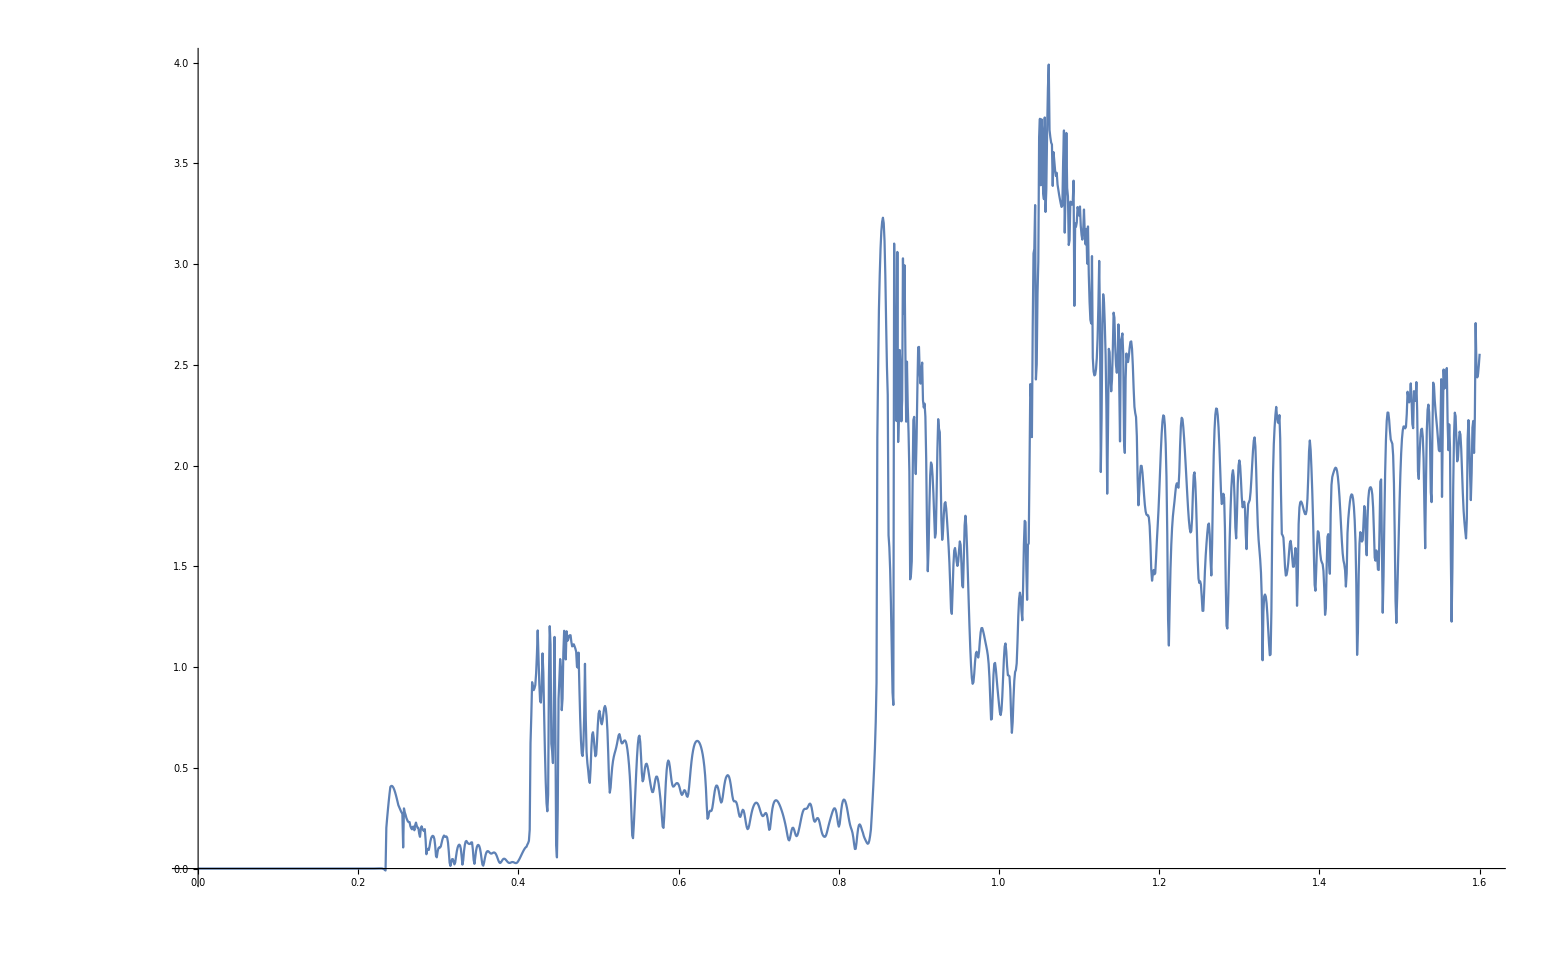

```mathematica
ListPlot[%83,Joined->True]
```

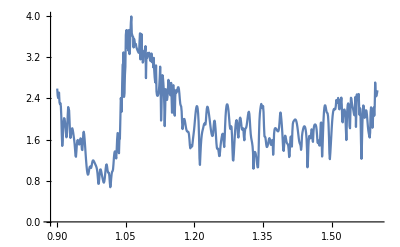

```mathematica
ListPlot[%79,Joined->True]
```

```mathematica
Integrate[Interpolation[%83][ω],{ω,0.0,1.6}]
```

1.71005

```mathematica
Table[{ω,deltae[0.5,ω]},{ω,Range[0,3,0.01]}]
```

```mathematica
tab=%99
```

{{0.,1.57326×10^-7},{0.01,3.52073×10^-7},{0.02,3.43657×10^-6},{0.03,9.11799×10^-6},{0.04,0.000017579},{0.05,0.0000291757},{0.06,0.0000444679},{0.07,0.0000642706},{0.08,0.0000897353},{0.09,0.000122475},{0.1,0.000164752},{0.11,0.000219774},{0.12,0.000292147},{0.13,0.000388624},{0.14,0.000519324},{0.15,0.000699848},{0.16,0.000955074},{0.17,0.00132635},{0.18,0.00188603},{0.19,0.0027696},{0.2,0.00425486},{0.21,0.00699302},{0.22,0.0128912},{0.23,0.0312319},{0.24,0.0949529},{0.25,0.127506},{0.26,0.121732},{0.27,0.198096},{0.28,0.0455448},{0.29,0.267539},{0.3,0.407934},{0.31,0.0136224},{0.32,0.862801},{0.33,0.862472},{0.34,0.111468},{0.35,0.112424},{0.36,0.382907},{0.37,0.364955},{0.38,0.66259},{0.39,0.775898},{0.4,0.710571},{0.41,0.382122},{0.42,0.446788},{0.43,0.094442},{0.44,0.278781},{0.45,0.684141},{0.46,0.0102275},{0.47,0.0544241},{0.48,0.930272},{0.49,1.01065},{0.5,0.36126},{0.51,0.261332},{0.52,0.654114},{0.53,0.462074},{0.54,1.04813},{0.55,0.221948},{0.56,0.579485},{0.57,0.82359},{0.58,1.39232},{0.59,0.637054},{0.6,0.739798},{0.61,0.857787},{0.62,0.0514375},{0.63,0.196755},{0.64,1.05873},{0.65,0.731483},{0.66,0.397082},{0.67,0.871568},{0.68,0.990576},{0.69,1.08795},{0.7,0.894719},{0.71,1.01411},{0.72,0.782692},{0.73,1.01092},{0.74,1.33516},{0.75,1.27593},{0.76,0.868919},{0.77,1.10827},{0.78,1.335},{0.79,0.978838},{0.8,1.13692},{0.81,0.754639},{0.82,1.59781},{0.83,1.25909},{0.84,1.2515},{0.85,0.292041},{0.86,0.604881},{0.87,0.509351},{0.88,0.0522701},{0.89,1.46819},{0.9,0.0862065},{0.91,0.933861},{0.92,0.859833},{0.93,0.670334},{0.94,1.12737},{0.95,0.56156},{0.96,0.400899},{0.97,1.2872},{0.98,0.84416},{0.99,1.63189},{1.,1.42588},{1.01,0.980047},{1.02,1.23012},{1.03,0.871396},{1.04,0.466974},{1.05,0.111316},{1.06,0.26083},{1.07,0.417501},{1.08,0.341257},{1.09,0.388669},{1.1,0.244135},{1.11,0.294404},{1.12,0.657075},{1.13,0.173708},{1.14,0.514423},{1.15,0.416539},{1.16,0.165812},{1.17,0.405112},{1.18,0.74219},{1.19,1.2302},{1.2,0.719967},{1.21,0.959246},{1.22,0.663693},{1.23,0.212551},{1.24,0.901421},{1.25,1.18396},{1.26,0.845631},{1.27,0.103299},{1.28,0.576726},{1.29,0.583805},{1.3,0.33822},{1.31,0.726545},{1.32,0.250113},{1.33,1.31131},{1.34,1.35611},{1.35,0.0162378},{1.36,1.03056},{1.37,0.88494},{1.38,0.623176},{1.39,0.415676},{1.4,0.885195},{1.41,0.855976},{1.42,0.429668},{1.43,1.04103},{1.44,0.594653},{1.45,0.954751},{1.46,0.838545},{1.47,1.05974},{1.48,1.17949},{1.49,0.304367},{1.5,0.707602},{1.51,0.032287},{1.52,0.155541},{1.53,0.529983},{1.54,0.787993},{1.55,0.505839},{1.56,0.411389},{1.57,0.434863},{1.58,1.00346},{1.59,0.804341},{1.6,0.202967},{1.61,0.260604},{1.62,0.196206},{1.63,0.743103},{1.64,0.426077},{1.65,0.0339077},{1.66,0.0425233},{1.67,0.0815576},{1.68,1.04924},{1.69,0.439754},{1.7,0.915628},{1.71,0.780619},{1.72,0.159893},{1.73,0.621635},{1.74,0.614105},{1.75,0.725487},{1.76,0.63667},{1.77,13.121},{1.78,0.89696},{1.79,0.543315},{1.8,0.899907},{1.81,0.0409881},{1.82,0.0881008},{1.83,0.00293511},{1.84,0.8168},{1.85,0.327264},{1.86,0.530387},{1.87,0.583761},{1.88,0.373433},{1.89,0.680551},{1.9,0.280284},{1.91,0.286564},{1.92,0.989673},{1.93,1.03859},{1.94,0.940373},{1.95,0.25004},{1.96,0.95316},{1.97,0.0652813},{1.98,0.282239},{1.99,1.14866},{2.,0.983888},{2.01,0.350118},{2.02,0.424021},{2.03,0.446803},{2.04,0.778589},{2.05,0.593947},{2.06,0.245146},{2.07,0.936946},{2.08,0.317634},{2.09,0.707207},{2.1,0.552747},{2.11,0.571595},{2.12,0.657641},{2.13,0.506494},{2.14,0.86962},{2.15,0.508953},{2.16,0.726532},{2.17,0.516774},{2.18,0.0288122},{2.19,0.319374},{2.2,0.325127},{2.21,0.479431},{2.22,0.257569},{2.23,0.484839},{2.24,0.771581},{2.25,0.292798},{2.26,0.0859224},{2.27,0.0289805},{2.28,0.276454},{2.29,0.883242},{2.3,0.0406588},{2.31,0.175941},{2.32,0.674344},{2.33,0.488165},{2.34,0.660406},{2.35,0.368911},{2.36,0.885808},{2.37,0.230826},{2.38,0.351636},{2.39,0.294657},{2.4,0.168084},{2.41,2.02744},{2.42,0.0131828},{2.43,0.0793661},{2.44,3.84534},{2.45,0.553508},{2.46,0.130634},{2.47,0.0307735},{2.48,0.183869},{2.49,0.149642},{2.5,0.0254463},{2.51,0.0451844},{2.52,0.0307366},{2.53,0.0303405},{2.54,0.20882},{2.55,0.134046},{2.56,0.0720118},{2.57,0.158411},{2.58,0.17192},{2.59,0.0646291},{2.6,0.471628},{2.61,0.164512},{2.62,0.290876},{2.63,0.0526562},{2.64,0.0912807},{2.65,0.310837},{2.66,0.47053},{2.67,0.107637},{2.68,0.818456},{2.69,0.975839},{2.7,0.568548},{2.71,0.516247},{2.72,0.774734},{2.73,0.0885289},{2.74,0.215831},{2.75,0.239616},{2.76,0.0799503},{2.77,0.0501677},{2.78,0.714035},{2.79,0.0796468},{2.8,0.0432892},{2.81,0.099831},{2.82,0.0628396},{2.83,0.0733866},{2.84,0.0400697},{2.85,0.00033289},{2.86,0.0000153071},{2.87,0.0000911163},{2.88,1.58423×10^-6},{2.89,6.77048×10^-6},{2.9,1.89299×10^-7},{2.91,2.24258×10^-7},{2.92,2.21904×10^-7},{2.93,2.05475×10^-7},{2.94,1.85057×10^-7},{2.95,1.64737×10^-7},{2.96,1.46055×10^-7},{2.97,1.29467×10^-7},{2.98,1.14977×10^-7},{2.99,1.02411×10^-7},{3.,9.15382×10^-8},{3.01,8.21285×10^-8},{3.02,7.39693×10^-8},{3.03,6.68745×10^-8},{3.04,6.06847×10^-8},{3.05,5.5265×10^-8},{3.06,5.05016×10^-8},{3.07,4.62994×10^-8},{3.08,4.25784×10^-8},{3.09,3.92714×10^-8},{3.1,3.63218×10^-8},{3.11,3.3682×10^-8},{3.12,3.13115×10^-8},{3.13,2.91762×10^-8},{3.14,2.72467×10^-8},{3.15,2.54982×10^-8},{3.16,2.39092×10^-8},{3.17,2.24613×10^-8},{3.18,2.11386×10^-8},{3.19,1.99272×10^-8},{3.2,1.88153×10^-8},{3.21,1.77924×10^-8},{3.22,1.68493×10^-8},{3.23,1.5978×10^-8},{3.24,1.51715×10^-8},{3.25,1.44236×10^-8},{3.26,1.37287×10^-8},{3.27,1.30821×10^-8},{3.28,1.24793×10^-8},{3.29,1.19166×10^-8},{3.3,1.13904×10^-8},{3.31,1.08977×10^-8},{3.32,1.04357×10^-8},{3.33,1.00018×10^-8},{3.34,9.594×10^-9},{3.35,9.2101×10^-9},{3.36,8.8483×10^-9},{3.37,8.50695×10^-9},{3.38,8.18453×10^-9},{3.39,7.87967×10^-9},{3.4,7.59113×10^-9},{3.41,7.31775×10^-9},{3.42,7.0585×10^-9},{3.43,6.81243×10^-9},{3.44,6.57865×10^-9},{3.45,6.35635×10^-9},{3.46,6.14482×10^-9},{3.47,5.94335×10^-9},{3.48,5.75133×10^-9},{3.49,5.56816×10^-9},{3.5,5.39333×10^-9},{3.51,5.22633×10^-9},{3.52,5.0667×10^-9},{3.53,4.91402×10^-9},{3.54,4.76789×10^-9},{3.55,4.62794×10^-9},{3.56,4.49383×10^-9},{3.57,4.36524×10^-9},{3.58,4.24188×10^-9},{3.59,4.12346×10^-9},{3.6,4.00972×10^-9},{3.61,3.90043×10^-9},{3.62,3.79536×10^-9},{3.63,3.69429×10^-9},{3.64,3.59703×10^-9},{3.65,3.50338×10^-9},{3.66,3.41318×10^-9},{3.67,3.32625×10^-9},{3.68,3.24244×10^-9},{3.69,3.16161×10^-9},{3.7,3.08361×10^-9},{3.71,3.00832×10^-9},{3.72,2.93561×10^-9},{3.73,2.86537×10^-9},{3.74,2.79749×10^-9},{3.75,2.73186×10^-9},{3.76,2.6684×10^-9},{3.77,2.607×10^-9},{3.78,2.54757×10^-9},{3.79,2.49004×10^-9},{3.8,2.43433×10^-9},{3.81,2.38036×10^-9},{3.82,2.32806×10^-9},{3.83,2.27736×10^-9},{3.84,2.2282×10^-9},{3.85,2.18052×10^-9},{3.86,2.13426×10^-9},{3.87,2.08937×10^-9},{3.88,2.04579×10^-9},{3.89,2.00347×10^-9},{3.9,1.96237×10^-9},{3.91,1.92244×10^-9},{3.92,1.88364×10^-9},{3.93,1.84592×10^-9},{3.94,1.80925×10^-9},{3.95,1.77359×10^-9},{3.96,1.7389×10^-9},{3.97,1.70515×10^-9},{3.98,1.67231×10^-9},{3.99,1.64034×10^-9},{4.,1.60921×10^-9}}

```mathematica
Table[{ω,Interpolation[tab][ω]},{ω,Range[0,3,0.001]}]
```

{{0.,1.57326×10^-7},{0.001,3.84169×10^-8},{0.002,-4.89597×10^-8},{0.003,-1.05096×10^-7},{0.004,-1.30286×10^-7},{0.005,-1.2482×10^-7},{0.006,-8.89936×10^-8},{0.007,-2.3098×10^-8},{0.008,7.25735×10^-8},{0.009,1.97728×10^-7},{0.01,3.52073×10^-7},{0.011,5.35316×10^-7},3978,{3.99,1.64034×10^-9},{3.991,1.63719×10^-9},{3.992,1.63405×10^-9},{3.993,1.63091×10^-9},{3.994,1.62779×10^-9},{3.995,1.62467×10^-9},{3.996,1.62156×10^-9},{3.997,1.61846×10^-9},{3.998,1.61537×10^-9},{3.999,1.61229×10^-9},{4.,1.60921×10^-9}}
 |  |  |  |

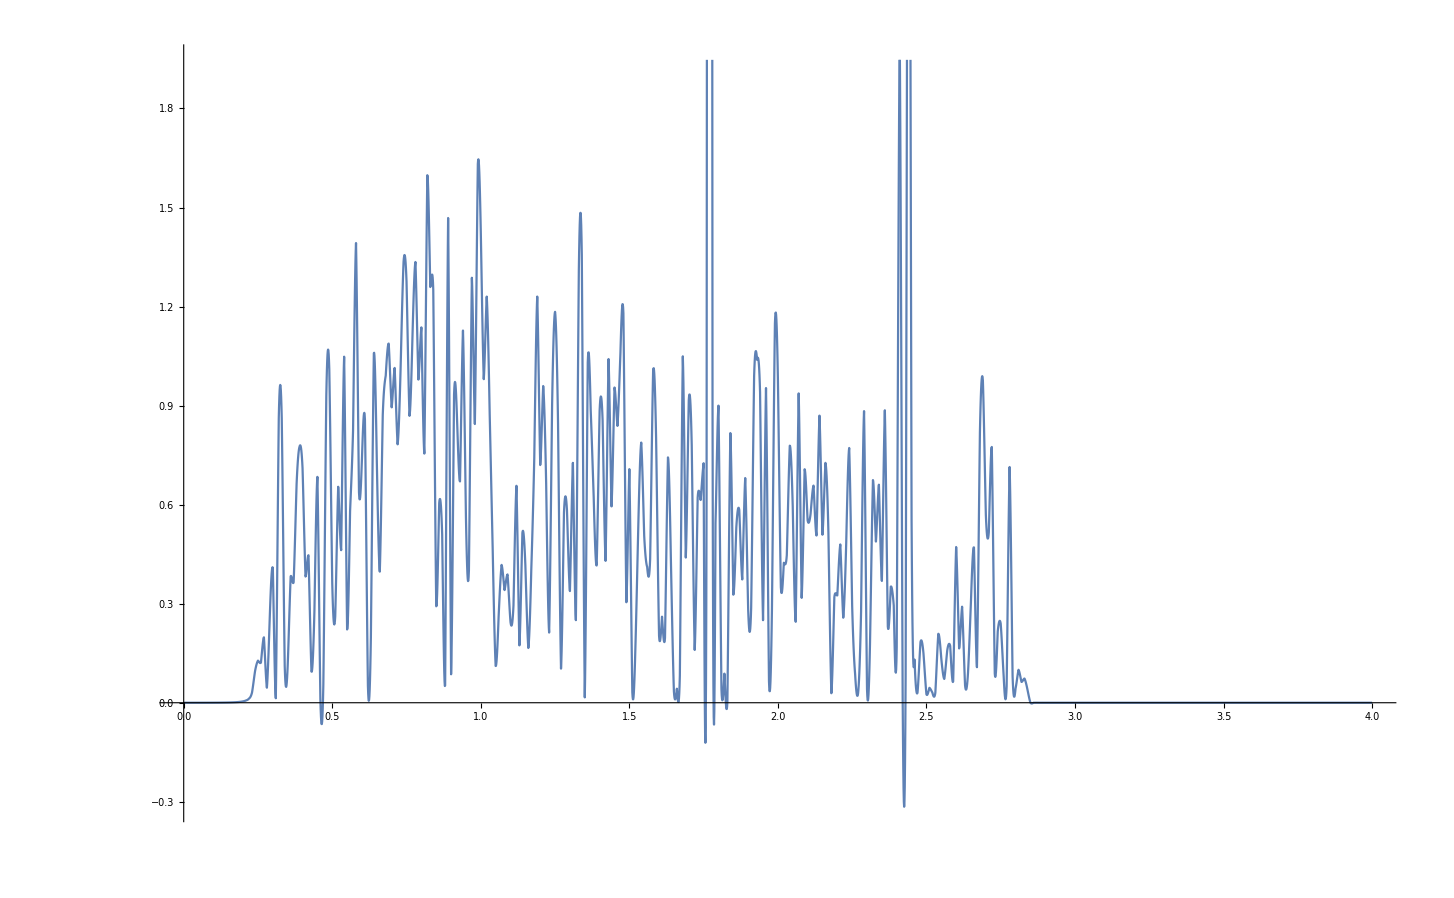

```mathematica
ListPlot[%102,Joined->True]
```

```mathematica
Table[{ω,ψ[ω]*(k00[[ω*1000+1]][[2]]-%102[[ω*1000+1]][[2]])},{ω,Range[0.0,3.8,0.001]}]
```

{{0.,-1.41741×10^-13},{0.001,-2.59666×10^-13},{0.002,-3.32105×10^-13},{0.003,-3.69439×10^-13},{0.004,-3.791×10^-13},{0.005,-3.65681×10^-13},{0.006,-3.31045×10^-13},{0.007,-2.7443×10^-13},{0.008,-1.92559×10^-13},{0.009,-7.97402×10^-14},{0.01,7.2024×10^-14},3779,{3.79,3.7701×10^-20},{3.791,3.73775×10^-20},{3.792,3.70393×10^-20},{3.793,3.66921×10^-20},{3.794,3.63416×10^-20},{3.795,3.5993×10^-20},{3.796,3.56518×10^-20},{3.797,3.53231×10^-20},{3.798,3.5012×10^-20},{3.799,3.47232×10^-20},{3.8,3.44616×10^-20}}
 |  |  |  |

```mathematica
Integrate[Interpolation[Table[{ω,ψ[ω]*(k00[[ω*1000+1]][[2]]-%102[[ω*1000+1]][[2]])},{ω,Range[0.0,3.8,0.001]}]][ω],{ω,0,3}]
```

2.69702

```mathematica
Integrate[Interpolation[Table[{ω,ψ[ω]*(tr[ω,0.0001,1,0]-deltae[0.5,ω])},{ω,Range[0.3,.8,0.001]}]][ω],{ω,0.3,0.8}]/Integrate[Interpolation[Table[{ω,ψ[ω]*ψ[ω]},{ω,Range[0.3,0.8,0.001]}]][ω],{ω,0.3,0.75}]+Integrate[Interpolation[Table[{ω,ψ[ω]*(tr[ω,0.0001,1,0]-deltae[0.5,ω])},{ω,Range[0.9,1.6,0.001]}]][ω],{ω,0.9,1.6}]/Integrate[Interpolation[Table[{ω,ψ[ω]*ψ[ω]},{ω,Range[0.9,1.6,0.001]}]][ω],{ω,0.9,1.5}]
```

6.52189

```mathematica
misfit[ϵ1_,x_,y_]:=Module[{Tin=T1[1],T=TT[1]},
tra:=Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{1,1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{2,2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{3,3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{4,4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{5,5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{6,6}}->ω+ⅈ*0.0001-ϵ1]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{7,7}}->ω+ⅈ*0.0001-ϵ1]]],
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{8,8}}->ω+ⅈ*0.0001-ϵ1]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{9,9}}->ω+ⅈ*0.0001-ϵ1]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{10,10}}->ω+ⅈ*0.0001-ϵ1]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{11,11}}->ω+ⅈ*0.0001-ϵ1]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{12,12}}->ω+ⅈ*0.0001-ϵ1]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{13,13}}->ω+ⅈ*0.0001-ϵ1]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-ϵ1]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]},
lista={{imp,imp3,imp11,imp,imp3,imp,imp,imp5,imp,imp,imp8,imp,imp,imp,imp6,imp,imp8,imp,imp,imp,imp1,imp,imp,imp,imp,imp2,imp6,imp,imp,imp,imp,imp,imp8,imp,imp,imp,imp,imp4,imp,imp,imp,imp,imp,imp,imp6,imp,imp,imp7,imp,imp,imp,imp,imp,imp4,imp6,imp14,imp,imp,imp,imp,imp6,imp,imp,imp,imp,imp,imp14,imp9,imp,imp,imp,imp4,imp,imp,imp,imp,imp,imp,imp8,imp13,imp,imp,imp,imp,imp2,imp,imp9,imp,imp13,imp,imp10,imp,imp,imp12,imp,imp,imp,imp,imp,imp}};b=Module[{},
(*Print[Dimensions[list]];*)sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,100}]; J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]];
b];
m5=Table[{ω,tra},{ω,Range[0,3,0.01]}];
υ=Module[{},
ρ2:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/14imp100.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ3:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/28imp100.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ4:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/42imp100.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ5:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/56imp100.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ6:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/70imp100.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ7:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/84imp100.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ8:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/100imp100.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ9:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/114imp100.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ10:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/126imp100.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ11:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/140imp100.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
list:={{1,ρ2},{2,ρ3},{3,ρ4},{4,ρ5},{5,ρ6},{6,ρ7},{7,ρ8},{8,ρ9},{9,ρ10},{10,ρ11}};
{Min[list],list[[Position[list,Min[list]][[1,1]],1]],list}];
υ]
```

```mathematica
misfit[0.5,1.5,0]
```

{0.0013329,2,{{1,0.0031443},{2,0.0013329},{3,0.0016147},{4,0.00242349},{5,0.00329677},{6,0.00404645},{7,0.00477011},{8,0.00558945},{9,0.005988},{10,0.00633344}}}

```mathematica
RandomSample[{imp,imp,imp,imp8,imp,imp,imp,imp14,imp,imp6,imp,imp,imp2,imp,imp,imp10,imp,imp,imp8,imp,imp,imp8,imp,imp,imp4,imp,imp3,imp,imp7,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp3,imp,imp1,imp,imp,imp6,imp12,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp13,imp,imp,imp,imp9,imp,imp11,imp,imp,imp,imp14,imp,imp,imp,imp8,imp,imp6,imp4,imp,imp,imp,imp,imp,imp,imp,imp13,imp,imp4,imp2,imp,imp,imp,imp9,imp,imp,imp,imp,imp,imp,imp5,imp,imp6,imp,imp,imp6}]
```

{imp,imp3,imp11,imp,imp3,imp,imp,imp5,imp,imp,imp8,imp,imp,imp,imp6,imp,imp8,imp,imp,imp,imp1,imp,imp,imp,imp,imp2,imp6,imp,imp,imp,imp,imp,imp8,imp,imp,imp,imp,imp4,imp,imp,imp,imp,imp,imp,imp6,imp,imp,imp7,imp,imp,imp,imp,imp,imp4,imp6,imp14,imp,imp,imp,imp,imp6,imp,imp,imp,imp,imp,imp14,imp9,imp,imp,imp,imp4,imp,imp,imp,imp,imp,imp,imp8,imp13,imp,imp,imp,imp,imp2,imp,imp9,imp,imp13,imp,imp10,imp,imp,imp12,imp,imp,imp,imp,imp,imp}

```mathematica
RandomSample[Join[RandomChoice[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp13,imp14},70],Table[imp,30]],100]
```

{imp,imp9,imp4,imp3,imp6,imp2,imp11,imp13,imp13,imp,imp,imp10,imp5,imp5,imp,imp5,imp14,imp14,imp6,imp,imp1,imp10,imp5,imp6,imp10,imp12,imp,imp,imp2,imp14,imp,imp2,imp,imp1,imp2,imp9,imp7,imp8,imp3,imp,imp,imp,imp10,imp6,imp14,imp,imp6,imp1,imp,imp5,imp3,imp,imp,imp13,imp,imp8,imp2,imp6,imp10,imp4,imp,imp,imp4,imp13,imp,imp13,imp,imp2,imp11,imp7,imp1,imp8,imp7,imp,imp,imp5,imp9,imp,imp7,imp3,imp13,imp,imp,imp5,imp13,imp9,imp4,imp,imp10,imp12,imp7,imp,imp6,imp,imp14,imp5,imp1,imp13,imp1,imp}